```mathematica
im=pgData["CEFI","Images","Swarm C","DateRange"->{{2022,1,22},{2022,1,23}}];
```

```mathematica
Length@im
```

1725

```mathematica
Manipulate[tiiImagePlot[im[[n]]],{n,1,Length@im,1}]
```

```mathematica
data=Transpose@Partition[im[[1394,1,3]],66];
```

```mathematica
Graphics[Raster[data,{{0,0},{40,66}},{0,1500},ColorFunction->"TemperatureMap"]]
```

-Graphics-

```mathematica
1024*768
```

786432

```mathematica
NotebookDirectory[]
```

/Users/john/src/tiim.dck/Mathematica/

```mathematica
Import[FileNameJoin[{NotebookDirectory[],"../example/A20220121_001120.png"}]]
```

```mathematica
data=Import[FileNameJoin[{NotebookDirectory[],"../example/SW_EFIA20220121_imaging_anomaly_stats.txt"}],"Table"]
```

{{secondsSince1970,PAH,PAV,MH,MV,CWH,CWV,UAWH,UAWV,LAWH,LAWV},{1642670019,0,0,0,0,0,0,0,0,1,1,0,1},{1642670051,0,0,0,0,0,0,0,0,1,1,0,1},{1642670083,0,0,0,0,0,0,0,0,1,1,0,1},1436,{1642745379,0,0,0,0,0,0,0,0,1,1,0,1},{1642745411,0,0,0,0,0,0,0,0,1,1,0,1},{1642745443,0,0,0,0,0,0,0,0,1,1,0,1},{1642745475,0,0,0,0,0,0,0,0,1,1,0,1}}
 |  |  |  |

```mathematica
data1=data[[2;;]];
data1[[All,1]]=data1[[All,1]]+AbsoluteTime[{1970}];
```

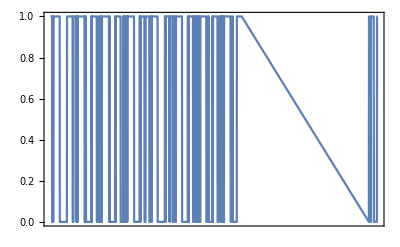

```mathematica
DateListPlot[N@data1[[All,{1,11}]],PlotRange->{{data1[[1,1]],data1[[-1,1]]},All}]
```

```mathematica
data1[[All,1]]
```

```mathematica
DateList[data1[[50,1]]]
```

{2022,1,22,6,49,7.}

```mathematica
data1[[2,
```